```mathematica
tmp={14808,13345,11925,10559,9257,8034,6895,5847,4827,4047,3298,2648,2093,1627,1243,932,686,495,349}
tmp2={14808,13345,11925,10559,9257,8034,6895,5847,4897,4047,3298,2648,2093,1627,1243,932,686,495,349}
```

{14808,13345,11925,10559,9257,8034,6895,5847,4827,4047,3298,2648,2093,1627,1243,932,686,495,349}

{14808,13345,11925,10559,9257,8034,6895,5847,4897,4047,3298,2648,2093,1627,1243,932,686,495,349}

```mathematica
dtmp=-Differences@tmp/tmp[[;;-2]]//N
dtmp2=-Differences@tmp2/tmp2[[;;-2]]//N
```

{0.0987979,0.106407,0.114549,0.123307,0.132116,0.141772,0.151994,0.174448,0.161591,0.185075,0.197089,0.209592,0.222647,0.236017,0.250201,0.263948,0.278426,0.294949}

{0.0987979,0.106407,0.114549,0.123307,0.132116,0.141772,0.151994,0.162476,0.173576,0.185075,0.197089,0.209592,0.222647,0.236017,0.250201,0.263948,0.278426,0.294949}

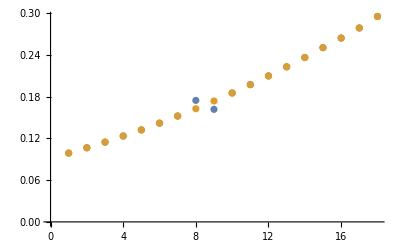

```mathematica
ListPlot[{dtmp,dtmp2}]
```